# 25: Eigenvalue Algorithms:

We know that we can not use the Characteristic Polynomial to compute eigenvalues. The question is how do we compute all the eigenvalues or more generally the eigen decomposition of a matrix A.

We are going to find out one way to compute roots of polynomials.

## Companion Polynomials

Matlab computes polynomial roots by building a matrix which has the same roots.  There are actually a whole bunch of these companion matrices for a given polynomial. The most common is implemented below

```mathematica
CompanionMatrix[a_]:= Module[{m=Length[a],A},
A=SparseArray[{Band[{2,1}]->1},{m-1,m-1}];
A⟦All,m-1⟧=-a⟦1;;-2⟧/a⟦-1⟧;
A
]
```

```mathematica
p[x_]:=2. x^2+3x +1 + x^7+π x^6
a=CoefficientList[p[x], x]
A=CompanionMatrix[a];
MatrixForm[A]
Sort[Eigenvalues[N[A]]]
Sort[x/.NSolve[p[x]==0,x]]
```

{1,3,2.,0,0,0,π,1}

(0 | 0 | 0 | 0 | 0 | 0 | -1
1 | 0 | 0 | 0 | 0 | 0 | -3
0 | 1 | 0 | 0 | 0 | 0 | -2.
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -π)

{-3.15322+0. ⅈ,-0.557703-0.0704326 ⅈ,-0.557703+0.0704326 ⅈ,-0.301024-0.891854 ⅈ,-0.301024+0.891854 ⅈ,0.864539-0.620724 ⅈ,0.864539+0.620724 ⅈ}

{-3.15322,-0.557703-0.0704326 ⅈ,-0.557703+0.0704326 ⅈ,-0.301024-0.891854 ⅈ,-0.301024+0.891854 ⅈ,0.864539-0.620724 ⅈ,0.864539+0.620724 ⅈ}

## Theorem 25.1: Galois

We all know the quadratic formula for the roots of a λ^2+b λ+c =0. There is a formula for the three roots of a cubic.  Here is one version!

```mathematica
Clear[a,b,c,λ]
λ/.Solve[λ^3+a λ^2+b λ+c==0,λ]
```

{-a/3-(2^(1/3) (-a^2+3 b))/(3 (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))+((-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(3 2^(1/3)),-a/3+((1+ⅈ √3) (-a^2+3 b))/(3 2^(2/3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))-((1-ⅈ √3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(6 2^(1/3)),-a/3+((1-ⅈ √3) (-a^2+3 b))/(3 2^(2/3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))-((1+ⅈ √3) (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))^(1/3))/(6 2^(1/3))}

There is a much longer formula for the four roots of a quartic

```mathematica
Clear[a,b,c,d,λ]
λ/.Solve[λ^4+a λ^3+b λ^2+c λ +d==0,λ]
```

{-a/4-1/2 √(a^2/4-(2 b)/3+(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))-1/2 √(a^2/2-(4 b)/3-(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))-1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3)-(-a^3+4 a b-8 c)/(4 √(a^2/4-(2 b)/3+(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3)))),-a/4-1/2 √(a^2/4-(2 b)/3+(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/2 √(a^2/2-(4 b)/3-(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))-1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3)-(-a^3+4 a b-8 c)/(4 √(a^2/4-(2 b)/3+(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3)))),-a/4+1/2 √(a^2/4-(2 b)/3+(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))-1/2 √(a^2/2-(4 b)/3-(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))-1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3)+(-a^3+4 a b-8 c)/(4 √(a^2/4-(2 b)/3+(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3)))),-a/4+1/2 √(a^2/4-(2 b)/3+(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/2 √(a^2/2-(4 b)/3-(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))-1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3)+(-a^3+4 a b-8 c)/(4 √(a^2/4-(2 b)/3+(2^(1/3) (b^2-3 a c+12 d))/(3 (2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))+1/(3 2^(1/3))(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d+√(-4 (b^2-3 a c+12 d)^3+(2 b^3-9 a b c+27 c^2+27 a^2 d-72 b d)^2))^(1/3))))}

Abel proved in 1824 that no such general formula can exist for higher degree polynomials!  See Theorem 25.1 for a careful statement of the theorem. What this means is that algorithms to compute eigenvalues need to be iterative like Newton’s method!

Computing eigenvalues using the characteristic polynomial is a bad idea because it would be unstable.  But it is even worse, Abel’s result means that there is no formula for non-tiny matrices.

## Iterative Schemes

Iterative schemes have some advantages

Black-box algorithms only use the matrix rather than work on the matrix.  This is essential to exploit sparsity! It also means they do not need to compute all the eigenvalues. Maybe you only care about the big ones!

You do not have to wait for full convergence if a “rough” answer will do.

Here is another iterative eigenvalue algorithm.  The power method one very different from Jacobi: Jacobi finds all the eigenvalues by operating on the matrix while the power method finds one particular eigenvalue by using the matrix.

### Power Method: A Simple Iterative Scheme

There is a simple way to compute the eigenvector associated with the largest eigenvalue of almost any matrix A. In words, multiply by A and normalize repeatedly.  This is very easy to code.

```mathematica
PowerMethod[A_][x_]:=Module[{z=A.x},z/Norm[z]]
```

It works!  Here is a simple test on an SPD matrix.

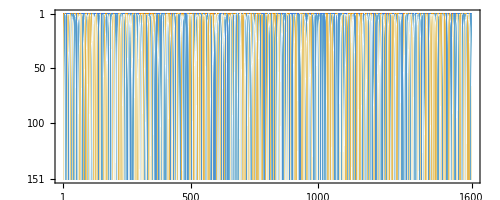

```mathematica
m=1600;
A=RandomReal[{-1,1},{m,m}];A=A.Aᵀ;
x0=RandomReal[{-1,1},m];PowerMethodData=NestList[PowerMethod[A], x0,150];
TableForm[PowerMethodData,TableHeadings->Automatic];
MatrixPlot[PowerMethodData]
```

It has almost converged to the eigenvector associated with the largest eigenvalue!

```mathematica
{{λ},{v}}=Eigensystem[A,1]
```

{{2099.75},{{0.0581204,-0.0169798,-0.00202559,0.0220097,0.0208473,0.00231036,-0.0262104,-0.0322346,0.0240567,-0.0305919,-0.0275986,-0.0244503,-0.0215367,0.0133842,-0.00383119,0.020107,0.0105233,-0.000341804,0.0320804,-0.0191682,-0.0554296,-0.0191386,0.0424919,0.00188057,-0.0597531,-0.0266122,0.00567583,-0.0202833,0.00351305,-0.0247777,-0.00256003,-0.032035,0.0308255,0.01161,-0.00712674,-0.0106904,0.0346963,-0.0102547,0.0266635,-0.00376057,0.00455369,-0.0171497,-0.003218,0.0174779,0.00425621,-0.00358937,0.0171736,0.00380662,-0.00787049,0.0766884,-0.00525952,0.0182696,-0.00230132,0.0342635,-0.000119115,0.025747,-0.00946007,0.000733511,-0.00787852,0.0194183,-0.0040146,0.0110939,-0.00063267,-0.00180142,0.00216055,0.0391588,0.00616282,0.000598239,0.00631642,-0.0296368,0.0264769,0.0304844,-0.0118822,-0.0364367,0.0174682,-0.00584686,0.0270409,-0.00917883,0.0033428,-0.0215275,-0.0188352,0.0350385,0.0163216,0.0345144,-0.0212709,-0.00750265,0.0173089,0.0355361,-0.0104831,-0.00329464,-0.0306322,0.0277628,0.00598838,-0.0464253,-0.0147323,0.00445346,-0.029388,0.0133701,0.0297012,0.00973667,-0.0120469,-0.00878021,-0.00678879,0.036005,-0.0161012,0.0150692,-0.0115207,-0.0538642,-0.0292641,-0.0205969,-0.0437706,-0.0617261,-0.011515,-0.0096938,-0.00383262,-0.0126309,-0.0141976,0.0121547,0.00100631,0.0074199,-0.0296215,-0.00231806,0.0272518,0.000728717,0.0232778,0.0420296,0.0132427,0.0297809,-0.000728769,0.0453439,-0.00217512,-0.0282414,-0.00561158,0.0237216,0.00239834,-0.0127878,-0.0143744,0.00865873,0.0318292,-0.0229148,-0.0336235,-0.0179272,-0.0221984,0.027536,0.0276671,0.0266255,0.0104406,-0.00537099,0.0135186,-0.00223851,-0.00872356,-0.0500425,0.0531059,0.0210556,-0.00362692,-0.00558331,-0.0344244,0.00726007,0.0175842,-0.0128581,-0.00629899,0.00252423,0.0262898,-0.0119797,0.00294231,0.0338747,0.0253222,-0.00529611,0.0356367,-0.0178207,0.0385264,0.0118247,0.00138856,-0.0164594,-0.00537084,0.00148938,-0.0109801,0.0122125,-0.0273211,-0.00293602,-0.0158338,-0.0273004,-0.0711165,-0.0324518,-0.00599784,0.0173116,0.00518276,0.0181546,-0.000558903,-0.00501902,0.00432224,-0.0202488,-0.0190763,0.00941562,0.0091276,0.0180604,0.0583501,-0.00607891,-0.00431531,0.0448263,0.00765452,-0.0158704,-0.0157006,-0.020637,0.0114865,0.0114589,0.0378085,0.0251013,0.0398817,-0.0272468,-0.00265251,-0.047009,-0.00688816,0.00178136,0.0293694,0.00803988,0.0626974,-0.0403574,0.0472596,-0.0181418,-0.000776169,-0.0132023,0.00602325,0.00201997,0.0172067,-0.00738091,0.00122548,-0.0115768,-0.0186124,0.0231263,0.00759475,0.0343592,0.0489167,-0.00497651,0.00644501,-0.0327956,-0.0118802,0.00291715,-0.0103599,0.0431263,-0.00417365,-0.0045227,-0.0256321,0.0343537,-0.00463944,0.0211735,-0.0327884,-0.0197308,-0.0314471,0.00446082,-0.0261859,-0.0354558,-0.0277358,-0.0577824,-0.0338574,-0.0311946,-0.00543452,0.0256225,-0.00838255,-0.0262716,0.00160072,0.0149349,0.00591148,-0.0189612,-0.0352921,0.00796269,0.0403691,-0.00735639,0.0244667,-0.0123172,-0.040301,-0.00389181,0.00316514,-0.0342846,-0.00154428,0.0214029,-0.0138397,-0.0529573,-0.0334665,-0.00740725,-0.0251395,-0.0250206,-0.0446138,0.0111666,-0.0306191,0.0130506,0.0494841,-0.0169054,-0.00165277,-0.0189026,0.0558898,-0.0163023,-0.00545778,-0.0184141,0.0273437,-0.000622855,-0.0115017,0.0112189,-0.0164394,-0.00499987,-0.0206324,0.0182482,-0.0196834,-0.00193328,0.0113378,-0.0268004,-0.0163331,-0.0137813,0.00560557,0.00899657,0.014971,0.00325823,-0.00854313,-0.0204899,-0.012112,0.0175593,0.0394794,-0.0134722,-0.0105228,-0.0212635,0.000103019,0.0167657,-0.0187402,-0.023055,-0.0106182,0.0610363,0.0384396,-0.00954697,-0.00985475,0.0103234,0.0314622,-0.00444427,-0.00299649,-0.0125565,-0.0463866,0.0101641,-0.0295924,-0.00592139,-0.0455357,0.0187679,0.0330788,-0.0100197,-0.00521466,0.0246523,0.00181574,-0.00903588,-0.00787793,-0.0244044,-0.0188607,0.00894376,-0.0116627,0.011165,-0.0166426,-0.0117886,-0.0403089,0.00245441,0.0278417,0.01366,0.000126977,0.000559456,-0.0161024,0.0166212,-0.0272862,0.000565582,0.00813345,-0.0293058,0.000706026,-0.00526528,-0.0452893,0.0425805,-0.00687933,0.0268069,-0.0336978,-0.0184289,-0.00967391,-0.0105808,-0.0160026,-0.0252891,-0.021836,-0.0016116,0.0334796,-0.0134262,-0.0406415,-0.0779359,-0.0250082,-0.0379251,-0.0217151,0.0293441,0.0127125,-0.00545454,0.000323864,-0.0281793,0.00540642,-0.0157013,0.0208196,-0.0167188,-0.0127478,0.0294529,0.0194454,0.0170299,-0.0292371,0.00155963,-0.00813362,0.0386611,0.0285384,0.0417444,0.0182668,-0.0298775,-0.0139964,0.0162494,0.0138581,-0.00544158,0.0418895,0.0310234,-0.0269086,0.0347567,0.0441743,-0.0172708,0.0136402,-0.046816,-0.0200458,-0.00977593,0.00560988,0.0136746,-0.028479,0.0485278,0.0398159,-0.018443,0.0116369,0.0371749,-0.0267478,0.0312026,-0.0123625,0.00725515,0.0242018,-0.0462609,-0.021839,0.0247306,0.00581187,0.0300171,-0.0234823,0.043546,0.0121776,-0.0460564,-0.0510614,0.000730144,-0.0151203,-0.0110123,-0.0677261,-0.0125933,-0.0193216,-0.0348066,0.00254714,0.00553369,-0.0221328,-0.00780023,0.0272071,-0.0146632,0.00162778,-0.0252344,0.0189477,-0.0279291,-0.0194271,0.0250303,-0.01328,0.021011,0.00777085,0.0173705,0.000204305,-0.0189344,0.0168696,-0.014034,-0.0429905,-0.00573408,-0.00903986,-0.0243632,0.066629,-0.00632739,0.00381147,-0.00660699,0.0348949,-0.0200055,0.00729555,0.0014933,0.00943685,-0.0112385,-0.0174162,-0.0502991,0.00449375,0.0139421,-0.0287457,0.0146664,0.0330139,0.0316157,-0.0181424,0.0208611,0.0187137,-0.011874,-0.0141814,0.0138642,0.0136027,0.0322124,0.0126367,-0.0381714,-0.0194531,0.0117868,-0.000977843,-0.0170205,-0.0014946,-0.0167318,-0.00292318,-0.0231116,0.0196825,-0.0161362,0.0344486,-0.0000876462,-0.0228861,-0.0214181,0.000698679,-0.000734239,-0.00688369,-0.0791428,-0.0525045,-0.0445094,0.00763204,-0.00594569,0.00822055,0.0144303,-0.051033,0.0163196,-0.0214279,-0.0119491,-0.0106795,-0.0178754,0.00898583,0.00333541,-0.00403114,-0.0309936,-0.00574025,-0.0238701,0.0180467,-0.0477732,0.00417298,-0.00306971,-0.0102793,0.025812,0.0218351,-0.00411698,0.0389035,-0.0157337,0.038303,0.00290446,0.0088757,0.0344196,-0.0309993,0.0006565,-0.0409733,0.0025092,-0.0429324,0.0162549,-0.00655722,0.0314326,-0.0278976,0.0187336,0.0126063,-0.0216978,0.0477771,0.0340735,0.030652,0.0260039,0.00602188,0.0320862,0.0330265,0.00384435,-0.049855,-0.00251371,-0.0214672,-0.0168627,-0.0125187,-0.0287907,0.0200953,-0.00500861,0.00538481,-0.00630172,-0.0235369,-0.0409059,0.0155329,-0.0236526,0.0235194,0.000228682,-0.0155791,0.0375207,0.00370871,-0.00058322,-0.00514421,0.0414886,0.00603517,0.0160415,-0.0382893,0.00388179,-0.0340109,0.0301916,-0.0230806,0.0232878,-0.0362725,0.0504903,-0.000871868,-0.0289966,-0.00468245,-0.0424347,-0.00119237,-0.0172476,0.00264869,0.00222027,0.040451,-0.00668635,0.0576441,-0.0337817,-0.0262387,-0.0085393,-0.00332117,0.0346089,0.0410414,-0.0273408,0.0351459,0.00551464,0.00111242,-0.00679085,-0.0267768,0.00444276,0.0211105,0.00467943,0.0421369,0.0490757,-0.0105399,-0.00428667,-0.0174176,-0.0252697,-0.0243738,-0.00348047,-0.0130003,0.0291483,0.0085568,0.0277358,-0.0267218,-0.00756856,0.0193017,-0.0833771,-0.00754491,0.0202155,-0.0402727,0.0757034,-0.0238304,0.000225929,-0.0097262,0.030422,0.0569274,0.0128751,0.015899,0.0139127,0.0729497,0.0265324,0.00806392,0.0266346,-0.0500417,0.0388829,-0.0358469,0.0263182,-0.0557982,-0.0280118,-0.0256261,0.0157065,-0.0275485,-0.00933923,0.0307947,0.00521268,-0.0116288,0.000724427,-0.0485411,0.028226,-0.00258761,0.0436324,-0.00159599,-0.0290096,-0.0666199,-0.0261629,0.0106087,-0.00869396,-0.0304975,-0.0115577,0.0033442,0.0428183,0.023072,0.0224423,0.0532151,0.0248764,-0.0162346,0.0319275,-0.00789226,0.000119337,-0.00380479,0.0250511,-0.00608137,0.0270105,0.0109683,0.00914853,0.00794782,0.0501484,0.0255406,-0.0128726,0.0320132,0.0142134,0.0193334,0.0366811,0.039978,0.00499819,0.0164502,-0.0242621,0.0325203,-0.000907704,-0.00756654,-0.00925248,0.0438098,0.0377462,0.0100085,-0.0317557,0.00886272,-0.00268664,0.0200631,0.0161975,0.0116716,0.00468343,0.00867835,0.068836,0.0435397,-0.00780044,0.0227494,-0.0472733,0.0199765,0.0167751,0.0200893,0.00437269,0.00157561,0.00590761,0.0550603,-0.00974703,-0.0169676,-0.00655023,0.0162173,0.010467,-0.00273788,-0.0425364,-0.00981115,-0.0371127,-0.00198402,-0.0344089,0.0343666,0.0430227,-0.0437278,-0.000768684,-0.0188474,0.0104577,-0.0186589,-0.0667517,0.0148307,0.0123164,0.0184169,-0.0083312,0.00925121,-0.0145017,0.052833,-0.0103781,0.000236012,-0.0111757,-0.00294061,0.031226,0.00259458,0.0349523,0.0536835,0.0152816,0.0104177,0.0347786,-0.030652,-0.0361952,-0.00270324,-0.0101471,0.006583,0.0390216,-0.0206833,0.0028619,-0.021714,0.0676661,-0.0272332,0.0246103,0.00494984,-0.0155103,0.0262304,0.00347782,-0.0104257,0.0328099,0.013814,0.0120491,-0.0104037,0.000584975,0.0528856,0.0101529,0.00218295,0.0301941,0.0318478,0.0104624,0.025016,0.0237037,-0.0273863,-0.00801549,0.0277541,0.011385,0.0102589,-0.0115256,0.00981075,-0.0401287,-0.00617269,-0.0126329,0.0359944,0.0152469,0.0158765,0.00399366,-0.00797502,-0.0206638,-0.00542747,-0.0333085,0.0337923,0.0328239,-0.0259224,-0.0229256,-0.0181707,0.0224675,0.0316338,-0.0132517,-0.0229391,0.00789676,0.00423715,0.0358917,-0.000855757,0.0208521,-0.0413693,-0.012065,0.00382897,0.0334585,-0.00207215,-0.00235443,-0.0139544,-0.00904465,0.00504826,0.0212228,-0.00206996,0.0100519,-0.0485675,-0.00341434,0.0165208,-0.00865494,0.00767833,-0.00219266,0.0113555,-0.0310005,0.0205023,0.000794051,-0.0126692,-0.00841583,0.0369249,0.00762324,0.019284,-0.00331831,0.00513123,0.0310359,-0.0026002,0.00933185,-0.00183109,-0.0163648,0.00571248,-0.00729202,0.00583312,0.00109299,-0.017409,0.0192804,0.0405056,0.0197084,-0.0284972,-0.0105987,-0.0283208,-0.0426698,0.00473841,-0.0134051,0.0194779,0.00449968,0.0196333,0.0248632,0.0215765,0.0471437,-0.0555906,-0.00404558,0.0185736,-0.0189262,-0.0443753,-0.00887845,0.0609507,-0.00739668,-0.046579,-0.0350909,-0.0189715,0.0140011,-0.040071,0.00954055,0.0477929,0.022346,0.0129019,-0.00197996,-0.0711027,0.0233443,-0.0579851,-0.00980128,0.000203644,0.0597256,0.0339821,-0.0223543,-0.0124988,-0.0153069,-0.0278485,-0.0181072,-0.000916631,-0.0059326,0.00383287,0.0148503,0.0222727,0.00442521,0.0256629,-0.00991245,0.0290889,-0.00691459,-0.00110907,0.035241,0.027085,0.00209861,-0.0313386,0.0208734,-0.000320371,0.00920852,0.0185059,0.00759736,0.00158276,0.00389128,-0.0375956,-0.0251168,0.0243595,0.0237382,-0.00360002,-0.00365494,-0.0104166,-0.0252426,0.0101908,-0.0216344,-0.0275627,-0.0303858,-0.0276535,0.0206689,0.0171622,0.0241233,0.0189761,0.00766296,-0.020288,-0.0431652,0.0341039,-0.0135332,-0.00739575,0.0149956,-0.00159007,-0.0141005,0.00222555,0.00208913,0.0127111,0.0141619,0.00886482,0.0454226,0.0144081,-0.022249,0.0652003,0.00830323,0.00762214,-0.0100551,0.0260638,-0.0371903,-0.0323705,0.03688,-0.0357244,0.00223678,-0.00322571,-0.0119372,-0.0225549,0.0160537,-0.00176456,0.0419074,0.0179832,0.0242773,0.0321917,0.0112803,0.0162142,0.00609444,-0.015881,0.00156373,-0.0344329,0.0192165,0.0346419,0.0177311,0.0406124,-0.00213122,-0.00843909,0.0457784,0.0142982,-0.0161035,-0.0620586,0.00273,-0.00419848,-0.0185021,0.0123105,0.0346428,-0.0282527,-0.00353367,-0.023853,-0.0311056,-0.00860585,0.0110518,0.0251649,0.00978471,0.0240393,-0.0380217,-0.0147892,-0.0132519,0.00392792,0.00906558,0.0333774,-0.0197846,-0.0114424,-0.0199561,-0.0151265,0.0124808,0.0233428,-0.00582969,-0.0191289,0.0175567,-0.0203541,-0.00911986,-0.0138536,-0.0213905,-0.0048225,0.0413328,-0.00182431,-0.00442093,0.0231673,-0.00652144,-0.00691133,-0.000999466,0.0219839,-0.0150595,0.00108844,0.0275179,0.00872516,0.00642582,-0.000380289,-0.0421516,-0.0491854,0.00656137,0.00476356,-0.0343068,-0.0191361,-0.00408177,0.00394111,-0.0130126,0.00335421,0.044023,-0.0239803,0.0260007,0.0132812,0.0406491,0.00130087,-0.00143919,-0.0192046,0.0238339,-0.0151703,0.00971723,-0.0168723,0.0267117,0.0144055,0.0000157928,-0.00495004,0.0447257,-0.046247,0.0395768,0.0165692,-0.0241365,0.0233472,0.0137082,-0.0157244,0.00238078,-0.0557661,-0.00741074,0.0214347,0.0263062,0.0050829,0.00534653,0.0166602,0.015082,-0.0311009,-0.0146159,-0.0360483,-0.0222157,0.025576,0.0288996,0.0314096,0.0101914,-0.0258276,-0.0306761,0.000355289,0.00862746,-0.0432604,0.000790949,0.0369974,0.0227124,0.0175629,0.00418099,0.0228491,-0.00217189,-0.00857436,-0.00532934,-0.00808226,-0.0286738,-0.0343292,0.0506909,-0.00263782,-0.00378897,-0.0348494,0.00964628,0.0234578,-0.00841897,-0.039168,-0.00648444,-0.0237354,0.0130376,0.0228454,0.0148086,0.0234932,0.0465896,0.0129319,-0.00561171,0.00453713,-0.0139027,-0.0104301,-0.00472224,0.0233321,-0.0360972,0.0014626,0.019787,-0.00779297,-0.00878612,0.0105563,0.00355064,0.051157,-0.0157328,-0.0301268,0.0322337,-0.0204072,-0.00189284,0.0216951,-0.0147386,-0.0077431,-0.0147487,-0.00668196,0.0218175,-0.0362071,-0.0246902,-0.00629847,-0.00342426,-0.0368994,0.0229553,-0.00463513,0.0191663,0.010118,-0.0181628,-0.00318484,0.0170355,0.0160812,0.0344137,-0.0225929,0.0117545,0.0353244,-0.0163257,0.0175327,0.00673154,0.0226241,0.00694832,0.0218128,0.0391201,0.0165019,-0.0189057,0.00511412,0.0145446,0.014477,0.0209768,0.0237482,0.00129181,0.0244699,0.0111228,-0.0222976,-0.0616607,-0.0101259,0.0408957,-0.00669429,0.0290788,0.00426164,0.00499221,0.0186149,0.042351,-0.002826,-0.0427564,-0.0417992,0.0422983,0.0164956,-0.0307442,-0.0191236,0.0313135,0.00741595,0.0146868,-0.030847,0.006158,-0.0101749,0.00805901,-0.0286406,0.0255003,-0.01703,-0.00124257,0.0222687,-0.0416082,0.00940303,-0.0195426,-0.00790603,-0.000147676,-0.0180394,0.00907789,-0.0414114,-0.0586507,-0.00425711,-0.0314346,0.0171363,0.00525283,0.00263021,0.00495001,-0.0388464,0.00991283,0.00508015,0.00743839,-0.0182873,0.0251283,-0.048055,0.0177734,-0.00684511,-0.0179583,-0.0189205,0.0299644,-0.0147577,-0.0376226,-0.00873921,0.0162264,0.0126166,-0.00482692,0.0226418,-0.00510386,0.0237283,0.0116404,0.013865,0.00582935,0.014273,0.00500437,0.0088489,-0.0000848297,0.0222359,0.041735,0.00461076,0.0335793,0.00655342,0.0207027,0.0475201,0.0645773,-0.000978708,-0.0729254,-0.00639274,0.00488068,0.0283621,-0.01276,0.00933503,-0.073665,-0.0415002,-0.00629053,0.000468722,-0.0231547,0.0549414,-0.0411931,0.0274597,-0.0126299,-0.0247404,0.045333,-0.00467181,0.000674274,-0.00911403,-0.000364098,0.0256634,-0.0300816,0.0174033,0.0329233,0.0211581,0.024715,0.0429922,0.0127442,-0.0146867,0.00425285,-0.000635388,0.0311452,-0.0549469,0.0138541,-0.00681194,0.00164883,0.0112139,0.0109847,0.0676344,-0.0106224,-0.00505304,0.00491622,0.0160547,0.00989704,0.0357473,-0.0155803,0.0245673,-0.0478509,-0.0247698,-0.0280087,-0.0227347,-0.0219148,0.0191194,0.0161521,0.0127689,-0.0352911,-0.0253727,0.0358794,-0.019341,0.0317218,0.00284216,-0.02787,0.00818379,0.0014779,-0.0124228,-0.0103428,-0.0294208,-0.000914774,0.0062491,0.0448322,-0.0235394,-0.0273599,0.00627846,0.0124337,0.00224102,0.00215392,0.00330059,0.00637806,-0.00105715,-0.0178976,-0.0366139,0.0186235,0.0209255,-0.0241389,0.00539686,0.0451049,-0.0484935,-0.00524833,0.0307698,0.00876194,0.000369534,0.027059,0.0240768,-0.00327912,0.043454,-0.016055,-0.0281926,0.00239623,-0.0400319,-0.0304246,0.00793833,0.0267241,-0.021067,0.00197243,-0.00295611,0.0108274,0.0569164,-0.00165497,-0.0258775,-0.0217559,-0.0899405,-0.0443193,-0.0086165,0.0425907,-0.0347734,0.00570762,0.00759331,0.00289468,-0.0354104,-0.0322944,0.00400243,-0.0247187,0.00534812,-0.0308055,0.0142304,0.0129209,-0.00899186,0.0411316,-0.0111734,0.060592,0.00901764,-0.0298564,0.0290988,-0.0256687,0.00162375,0.0218305,-0.0661718,-0.0253598,-0.0364129,-0.00357455,0.0138244,0.0235303,0.0029341,0.0208109,0.00281677,-0.0157574,0.0133665,0.00934822,0.0190983,0.0298789,0.0123939,-0.00936702,-0.00519219,0.0443938,-0.00908169,-0.0033771,0.0142558,0.0330049,0.0392713,-0.0193918,0.0179906,0.0149831,0.0359323,-0.0287637,0.0164409,-0.0106367,-0.0124154,0.00107011,-0.0449652,0.0215696,0.000155344,0.0366324,0.0390154,-0.050191,-0.0409025,0.00839992,0.0300417,-0.00210097,-0.0161568,0.0140548,0.0134192,-0.0072371,0.00735538,0.034565,-0.0214246,-0.00878084,-0.016679,-0.0537432,-0.000113927,0.0170727,-0.00107901,0.0087335,-0.00124161,-0.0247105,-0.0185139,0.00968102,0.0097682,-0.0323942,-0.0237637,0.000915847,-0.0276893,0.00441197,0.0261735,-0.0133385,0.0239299,-0.0288271,-0.0330769,-0.0183575,0.0204009,-0.0248232,0.0349203,-0.00914924,-0.0343349,-0.0124457,-0.00699433,0.0357478,0.0228214,0.015668,0.0334105,0.00566331,-0.0244891,-0.00529065,-0.0564679,-0.00822385,0.000541349,0.00609837,-0.0145484,0.0249327,0.0183791,0.0284589,0.00226122,0.0325744,-0.0586402,0.00785173,-0.00291515,0.0457068,-0.048819,0.0101581,0.0365525,-0.0436681,-0.00291792,-0.0348577,0.0100962,-0.0366807,-0.000568346,0.0140317,0.0612076,-0.0230003,-0.00289458,-0.0289,0.015997,0.0214956,0.00253891,0.0166314,-0.0423747,0.0314051,0.0300699,0.00715417,0.0365247,-0.0148739,-0.00714862,0.00384121,0.0359143,0.00833197,-0.0263689,-0.0171803,0.036118,-0.0326371,-0.00798803,-0.0246212,0.026574,0.000649513,-0.0441251,-0.0553712,0.0106391,-0.00860246,-0.0145425,0.0220741,-0.0165337,-0.00445477,0.0324644,0.0189396,0.0289999,-0.0167075,-0.0137483,0.0195306,0.0198657,-0.0163433,0.00669959,-0.025683,0.0231874,-0.0112225,0.0391995,0.011726,0.0224462,-0.00615845,0.0218789,-0.0422353,0.0119548,0.0361688,0.00707989,-0.00476501,-0.0345644,0.0109148,-0.0399823,0.00420738,0.0427462,-0.0220064}}}

```mathematica
vv=PowerMethodData⟦-1⟧;
(A.vv)/vv
```

{2097.09,2096.28,2091.39,2091.92,2091.02,2092.88,2093.49,2095.43,2061.2,2095.95,2110.01,2147.9,2088.58,2159.54,2090.88,2128.78,2089.05,2090.03,2115.32,2086.95,2095.49,2085.42,2057.39,2072.41,2100.56,2081.61,2087.92,2092.69,2089.05,1947.53,2131.87,2100.36,2084.63,2072.09,2091.03,2088.52,2096.19,2074.79,2091.88,2087.03,2088.63,2093.56,2095.24,2078.68,2080.4,2090.67,2075.93,2093.93,2096.11,2100.43,2202.31,2099.96,2093.98,2080.02,2095.16,2106.38,2069.25,2090.31,2107.96,2095.98,2089.05,2093.88,2064.2,2088.28,2111.82,2095.07,2094.07,2095.11,2085.98,2113.33,2091.55,2107.08,2102.58,2108.28,2110.27,2089.17,2088.07,2092.92,2233.34,2097.19,2068.86,2092.89,2119.17,2072.9,2204.95,2095.49,2097.7,2092.41,2081.93,2089.06,1833.99,2095.61,2087.28,2092.51,2062.96,2097.14,2094.22,2091.65,2092.35,2092.92,2088.04,2085.37,2098.73,2092.95,2094.45,2106.17,2095.72,2062.69,2075.31,2057.69,2074.47,2094.17,2098.,2083.77,2113.49,2119.72,2082.42,2089.46,2077.22,2091.67,2097.39,2068.02,2091.63,2084.58,2102.23,2009.01,2093.72,2093.56,2088.54,2091.05,2078.68,2081.2,2089.17,2092.32,2078.91,2085.71,2094.89,2089.8,2084.91,2091.23,2066.87,2094.35,2088.45,2065.88,2044.92,2096.45,2099.24,2205.88,2092.61,2084.2,2085.15,2095.15,2245.77,2111.72,2110.53,2094.34,2093.93,2087.82,2094.48,2088.41,2088.37,2090.41,2089.08,2093.86,2090.58,2106.04,2060.99,2082.57,2094.83,2117.23,2113.36,2093.12,2089.55,2094.25,2051.12,2086.15,2089.93,2060.32,2093.25,2082.14,2085.44,2099.41,2095.36,2087.63,2095.27,2089.14,2092.85,2192.53,2092.77,2089.89,2098.99,2088.81,2089.78,2088.14,2089.8,2098.63,2116.68,2091.23,2097.13,2103.99,2088.93,2092.94,2091.35,2098.42,2123.58,2040.91,2094.69,2091.77,2080.27,2152.53,2083.8,2092.62,2093.57,2090.46,2093.72,2104.21,2102.91,2088.27,1888.12,2093.37,2092.8,2083.81,2086.74,2095.61,2088.1,2083.97,2095.,2083.93,2131.72,2091.99,2095.,2058.59,2099.25,2085.69,2105.32,2087.46,2095.68,2093.01,2097.91,2095.46,2081.41,2123.37,2087.65,2104.41,2094.09,2096.82,2090.2,2097.72,2075.79,2084.52,2105.48,2103.07,2100.57,2097.75,2100.15,2104.53,2099.69,2106.11,2101.91,2161.23,2083.02,2095.35,2074.1,2107.28,2096.77,2090.81,2064.62,2090.73,2131.39,2090.25,2304.52,2093.7,2096.,2096.82,2083.33,2046.92,2092.47,2006.,2078.35,2186.36,2090.37,2114.76,2079.04,2107.64,2091.06,2083.07,2094.46,2089.11,2092.03,2093.47,2104.24,2102.39,2090.78,2083.67,2083.17,2092.72,2086.84,2086.31,2067.02,2126.31,2089.42,2089.57,2083.35,2073.98,2091.94,2070.39,2097.88,2083.24,2090.18,2091.81,2130.47,2108.44,2104.98,2093.23,2056.68,2070.61,2156.16,2104.99,2092.97,2094.82,2089.71,2087.13,2039.18,2101.15,2077.87,2109.06,2104.93,2088.06,2103.41,2090.14,2143.5,2089.76,2091.79,2103.91,2084.89,2086.63,2088.,2091.7,2103.63,2088.,2095.88,2089.92,2086.78,2098.05,2048.77,2112.24,2080.13,2097.07,2049.62,2115.48,2095.26,2114.84,2089.92,2198.33,2055.48,2024.66,2141.7,2086.8,2087.33,2090.86,2092.96,2091.66,2108.3,2090.02,2087.62,2073.53,2424.59,2088.41,2094.57,2092.44,2085.75,2096.91,2061.14,2092.13,2078.41,2089.61,1907.69,2095.24,2135.04,2091.24,2094.31,2089.19,2113.74,2104.3,2095.61,2114.53,2104.1,2097.44,2103.09,2109.64,2106.3,2098.58,2094.31,2095.76,2091.51,2386.93,2101.05,2082.14,2085.85,2088.08,2094.32,2093.58,2001.16,2094.41,2095.17,2068.61,2090.49,2092.46,2072.35,2095.03,2088.49,2084.19,2076.96,2094.16,2092.17,2083.76,2094.45,2090.93,1966.12,2098.32,2106.09,2091.12,2079.9,2090.71,2078.06,2091.9,2100.02,2092.41,2078.65,2096.37,2088.08,2073.93,2093.32,2091.35,2089.65,2092.78,2100.13,2095.41,2101.73,2093.81,2091.11,2100.26,2089.82,2091.97,2099.02,2092.39,2086.2,2088.92,2147.06,2049.72,2092.26,2091.31,2082.9,2088.57,2117.11,2083.9,2080.32,2073.23,2101.49,2089.82,2099.46,2097.51,2084.54,2093.04,2089.73,2081.2,1901.84,2100.9,2097.25,2095.02,2073.15,2071.9,2127.61,2091.51,2141.96,2094.06,2096.08,2069.46,2091.95,2090.76,2090.16,2090.52,2096.78,2090.33,2094.06,1984.71,2090.71,2096.23,2082.68,2093.19,2110.49,2087.68,2083.6,2101.73,2101.78,2091.99,2088.97,2083.94,2069.87,2069.95,2087.33,2089.85,2092.28,2093.85,2091.88,1163.61,2088.55,2096.71,2093.29,2092.73,2085.15,2086.47,2092.6,2089.34,2099.31,2096.71,2063.76,2084.4,2090.03,2095.49,2090.6,2104.82,2119.54,2127.6,2087.14,2095.09,2090.16,2075.84,2097.61,2085.,2076.26,2089.21,2084.76,2104.02,1925.43,2088.51,2083.97,2164.46,2207.69,2072.27,1996.92,2092.68,2089.35,2095.64,2361.13,2112.83,2078.75,2089.71,2091.25,2082.19,2098.53,2098.85,2097.15,2095.98,2097.94,2085.77,2099.02,2087.67,2099.63,2080.75,2094.69,2138.96,2092.63,2089.73,2089.95,2100.44,2093.99,2095.44,2093.9,2070.64,2094.38,2085.95,2092.07,2089.94,2165.04,2090.65,2097.28,2084.95,2080.12,2023.36,2081.77,2091.35,2087.36,2084.53,2086.76,2110.62,2079.88,2091.88,2033.36,2091.95,2096.53,2093.93,2088.2,2089.36,2045.26,2100.21,2083.1,2091.84,2093.19,2076.19,2087.07,1452.78,2091.86,2096.02,2099.16,2121.52,2085.78,2083.47,2137.88,2072.47,2089.61,2091.27,2091.38,2096.88,2093.74,2110.43,2101.91,2087.89,2109.52,2090.16,2089.6,2058.83,2103.12,2101.85,2099.9,2084.9,2095.11,2090.66,2098.53,2055.48,2091.67,2091.62,2101.95,2098.65,2087.44,2083.37,2092.2,2063.96,2097.28,2090.55,2094.82,2109.14,2084.35,2079.49,2081.69,2069.3,2088.34,2092.46,2220.11,2045.,2093.32,2102.29,2092.74,2076.11,2080.1,2065.39,2093.92,2071.86,2086.22,2089.68,2094.7,2120.,2096.19,2077.19,2094.6,2098.2,2092.41,2095.42,2099.68,2093.86,2114.32,2081.72,2097.65,2091.41,2094.72,2090.52,2095.15,2094.38,2095.63,2101.99,2097.81,2070.48,2080.23,2093.13,2096.01,2090.92,2081.87,2091.07,2094.5,2086.23,2099.28,2113.37,2089.46,2116.84,2106.01,2096.93,2280.31,2021.42,2089.61,2082.64,2096.22,2127.43,2106.62,2092.3,2084.41,2086.19,2093.47,2102.25,2061.32,2096.16,2097.53,2052.64,2106.33,2098.11,2091.44,2091.93,2089.1,2093.83,2135.53,2077.61,2097.79,2022.06,2108.09,2093.64,2091.02,2101.83,2104.98,2095.98,2098.58,2031.68,2091.35,2090.75,2088.23,1975.59,2072.11,2089.02,2092.36,2094.1,2095.96,2093.49,2100.25,2093.55,2092.78,2091.2,2120.78,2090.93,2084.12,2091.01,2057.42,2089.86,2090.93,2036.69,2072.44,2109.67,2090.52,2086.56,2096.69,2095.93,2082.85,2091.63,2083.38,2086.85,2076.56,2095.55,2091.34,2056.96,2092.14,2071.23,2074.43,2052.14,2067.95,2089.04,2104.94,2086.79,2114.37,2101.52,2090.43,2093.51,2098.34,2086.6,2092.23,2092.04,1955.64,2075.84,2081.13,2089.69,2084.03,1937.91,2088.68,2084.89,2094.2,2096.67,2086.34,2094.53,2083.82,2107.57,2078.88,2091.47,2088.76,2105.49,2130.26,2083.17,2106.06,2086.81,2106.3,2093.61,2088.69,2084.53,2121.96,2074.73,2099.49,2088.03,2066.92,2088.98,2072.22,2082.1,2096.87,2094.86,2087.21,2097.44,2088.49,2087.86,2090.99,2056.98,2102.08,2039.43,2092.38,2093.23,2096.26,2107.38,2093.45,-7195.44,2087.11,2098.07,2090.5,2101.4,2092.81,2087.36,3476.46,2075.65,2086.93,2101.45,2098.9,2084.22,2090.34,2108.7,2078.28,2892.25,2087.05,2100.18,2076.26,2086.62,2090.53,2086.27,2087.49,2085.86,2097.19,2089.13,2093.65,2088.29,2127.41,2088.56,2089.27,2093.32,2084.62,2091.86,2091.17,2088.49,2084.94,2085.04,2101.07,2085.03,2087.82,2069.65,2075.37,2113.65,2103.34,2090.73,2106.34,2082.63,1923.97,2395.72,2082.82,2081.47,2092.2,2085.38,2092.31,2087.1,2094.32,2051.49,2091.41,2093.52,2085.4,2069.7,2082.04,2082.27,2075.52,2085.94,2108.64,2116.12,1455.64,2115.29,2096.29,2089.08,2099.61,2054.66,2098.32,2093.29,2093.82,2087.65,2296.79,2072.35,2097.56,2094.84,2092.99,2076.86,2098.31,2093.97,2096.47,2089.59,2092.46,2118.84,2065.59,2087.61,2094.23,2088.78,2104.27,1985.79,2106.26,2090.66,2084.95,2091.37,2097.19,2091.22,2094.06,2078.76,2104.26,2090.94,2115.88,2087.55,2089.53,2089.18,2091.19,2085.97,2095.99,2094.55,2100.3,2100.08,2093.55,2090.02,2101.25,2091.26,2092.1,2097.77,2083.21,2093.73,2089.08,2143.19,2072.06,2089.43,2082.8,2093.87,2090.65,2098.32,2076.58,2097.11,2091.16,2087.91,2130.75,2090.83,2024.98,2097.8,2086.77,2086.27,2108.4,2094.87,2185.82,2133.87,2088.23,2056.98,2119.05,2144.02,2113.04,2096.75,2103.65,2090.31,2093.23,2091.95,2087.4,2097.17,2054.07,2120.81,2105.16,2115.22,2090.89,2092.56,2133.45,2086.62,2099.46,2079.57,2101.94,2055.04,2087.35,2094.58,2082.29,2077.83,2088.99,2087.26,2096.08,2093.56,2097.35,2085.34,2179.83,2099.04,2089.04,2190.68,1783.51,2084.11,2099.15,2090.95,2194.04,2120.8,2087.94,2076.03,2095.73,2096.23,2089.97,2085.63,2090.87,2092.72,2079.7,2090.31,2112.32,2064.,2084.03,2095.01,2094.58,2092.6,2095.03,2267.42,2090.33,2090.48,2156.52,2102.69,2091.67,2098.15,2106.84,2093.2,2093.09,2104.89,2088.8,2101.91,2089.6,2075.06,2098.22,2087.27,2157.62,2097.67,2039.53,2088.04,2095.5,2092.91,2085.33,2083.75,2097.38,2127.56,2077.5,2095.33,2083.74,2116.83,2092.52,2089.77,2095.43,2093.95,2099.52,2095.45,2087.08,2079.71,2082.09,2094.65,2149.07,2104.58,2090.69,2089.67,2090.85,2094.34,2088.7,2093.95,2098.05,2089.78,2091.84,2086.68,2100.53,2099.67,2108.71,2116.67,2096.49,2089.03,2099.88,2088.15,2098.48,2102.42,2098.21,2047.94,2100.45,2095.3,2083.45,2082.05,2066.53,2092.28,2099.3,2088.7,2090.75,2096.29,2076.84,2079.69,2097.49,2085.47,2081.93,2060.24,2935.53,2087.58,2094.93,2093.29,2095.17,2091.34,2089.36,2051.1,2089.37,2089.26,2102.28,2082.92,2088.95,2094.24,2109.2,2092.06,2090.42,2090.07,2090.54,2078.34,2091.31,2078.35,2096.7,2107.97,2090.95,2086.61,2103.09,2087.37,2088.49,2095.07,2094.33,2091.28,2393.98,2060.23,2089.1,2079.14,2088.93,2095.14,2090.88,2092.66,2100.63,2086.54,2087.24,2096.19,2092.99,2091.15,2093.67,2087.28,2089.12,2092.48,2089.14,2092.43,2095.89,2092.44,2079.58,2092.4,2093.64,2092.36,2086.14,2084.41,2102.73,2090.23,2099.13,2100.36,2109.39,2088.45,2105.97,2086.43,2090.84,2074.45,2077.19,2092.09,2099.5,2089.9,2079.56,2067.08,2100.31,2075.87,2263.08,2088.47,2092.38,2098.57,2110.76,2073.8,1902.65,2094.47,2085.93,2064.72,2089.23,2090.58,2096.49,2099.82,2091.96,2070.51,2073.86,2099.51,2058.68,2088.15,2105.67,2093.23,2091.67,2103.58,2091.78,2018.19,2097.45,2129.42,2092.02,2076.38,2095.61,2100.28,2123.55,2100.63,2098.14,2090.02,2107.08,2060.66,2086.27,2172.03,2099.24,2064.56,2113.11,2092.16,2095.29,2094.81,2091.54,2092.27,2095.7,2077.7,2092.93,2088.51,2100.8,2099.48,2089.99,2090.38,2675.22,2089.6,2049.7,2084.47,2091.41,2091.47,2110.35,2090.81,2094.,2088.7,2092.03,2073.94,2113.6,2095.64,2087.88,2089.84,2084.58,2085.21,1921.79,2081.11,2099.13,2087.8,2091.89,2091.26,2097.79,2092.35,2246.44,2061.58,2099.83,2108.13,2089.47,2091.91,2094.6,2093.34,2086.35,2093.87,2086.9,2098.12,2086.51,2084.23,2101.4,2090.1,-5207.26,2108.82,2095.36,2103.79,2077.86,2092.69,2097.09,2098.42,2094.25,2091.88,1977.39,2144.,2076.67,2088.85,2074.5,2083.87,2066.05,2098.56,2095.89,2079.83,2034.23,2032.,2112.69,2088.74,2091.16,2086.23,2091.55,2093.18,2091.44,2093.05,2083.65,2082.94,2083.96,2087.88,2093.78,2094.4,2094.28,2110.61,2061.27,2094.99,2090.91,2091.12,2079.68,1886.21,2104.06,2092.28,2085.35,2090.99,2095.81,2104.99,2095.46,2098.47,2091.57,2094.02,2103.99,2084.01,2086.73,2094.02,2082.33,2084.88,2109.76,2089.45,2077.39,2090.16,2089.26,2051.94,2084.64,2093.68,2086.88,2092.81,2059.2,2100.07,2067.28,2092.64,2085.42,2091.26,2129.05,2094.29,2076.51,2088.61,2082.82,2095.97,2094.67,2090.16,1975.08,2081.12,2088.44,2092.65,2093.21,2089.57,1976.49,2077.34,2096.14,2091.94,2114.3,2026.26,2091.11,2089.02,2094.14,2082.33,2077.63,2083.21,2093.68,2094.44,2091.1,2101.4,2100.52,2092.19,2091.15,2079.72,2081.78,2092.62,2002.91,2084.86,2055.29,2095.95,2080.85,2074.05,2095.38,2080.38,2092.33,2095.31,2072.6,2092.06,2091.17,2091.85,2089.95,2111.97,2108.41,2135.06,2092.12,2092.17,2094.55,2092.2,2079.94,2086.26,2094.65,2096.24,2094.66,2053.21,2098.12,2045.05,2084.35,2083.36,2090.87,2090.19,2147.44,2095.67,2085.09,2101.68,2172.47,2089.86,2102.72,2097.34,2107.17,2094.,2092.91,2087.83,2081.48,2077.05,2093.29,2090.57,2084.8,2087.92,2147.76,2091.45,2077.45,1620.55,2087.63,2081.45,2094.01,2093.08,2083.47,2089.15,2090.33,2096.29,2088.13,2092.27,2077.02,2087.93,2129.49,2097.77,2091.33,2099.14,2087.64,2088.58,2090.25,2092.28,2097.26,2095.43,1430.77,2105.11,2092.87,2159.29,2101.66,2083.65,2060.3,2095.86,2096.71,2094.45,2095.2,2116.35,2092.45,2079.31,2073.24,2089.23,2094.58,2087.65,2093.04,2088.74,2085.53,2078.95,2093.51,2087.76,2104.14,2069.98,2101.76,1920.81,2092.86,2091.73,2089.1,2314.64,2073.12,2076.42,2085.21,2101.82,2055.14,2103.99,2093.36,2084.16,2091.93,2094.58,2120.81,2093.83,2104.44,2096.59,2094.49,2008.5,2085.06,2093.62,2089.22,2088.4,2107.03,2059.45,2092.08,2092.71,2080.36,2114.11,2097.51,2086.28,2093.69,2098.9,2091.46,1957.92,2093.3,2089.18,1294.38,2003.62,2097.88,2096.55,2110.2,2090.1,2076.49,2101.07,2096.58,2055.66,2103.47,2089.09,2080.24,2096.99,2094.11,2307.71,2088.86,2089.09,2098.79,2099.57,2102.41,2099.38,2076.44,2084.75,2088.9,2078.69,2029.1,2050.8,2088.32,2084.44,2079.72,2086.13,2092.51,2081.74,2092.96,2086.93,2081.79,2091.42,2094.06,2099.1,2084.48,2090.11,2091.67,2087.7,2093.2,2086.4,2064.1,2087.61}

```mathematica
{18.782680833027204,18.78267992377554,18.782691955769128,18.782640469938702,18.782677319405842,18.78266970926498,18.782679702106222,18.782671252773063,18.782688903488058,18.782674831333594,18.78267562671868,18.782684167730785,18.78267199699047,18.782672394627376,18.78267214569421,18.782682632835648}
```

It also works more generally! Here it is on a general symmetric matrix.

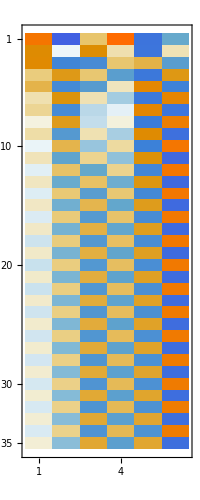

```mathematica
m=6;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
x0=RandomReal[{-1,1},m];PowerMethodData=NestList[PowerMethod[A], x0,34];
TableForm[PowerMethodData,TableHeadings->Automatic];
MatrixPlot[PowerMethodData]
```

It also frequently (but not always) works on a general matrix.

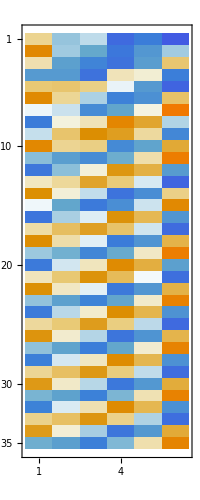

```mathematica
m=6;
A=RandomReal[{-1,1},{m,m}];
x0=RandomReal[{-1,1},m];PowerMethodData=NestList[PowerMethod[A], x0,34];
TableForm[PowerMethodData,TableHeadings->Automatic];
MatrixPlot[PowerMethodData]
```

```mathematica
Eigenvalues[A]
```

{-0.0112842+1.01217 ⅈ,-0.0112842-1.01217 ⅈ,0.746479+0.47494 ⅈ,0.746479-0.47494 ⅈ,-0.583088+0. ⅈ,0.220174+0. ⅈ}

```mathematica
vEnd=PowerMethodData⟦-3;;-1⟧
```

{{0.327082,-0.493079,-0.114887,0.137063,-0.7846,-0.0480398},{0.651219,-0.182544,0.161783,0.704838,-0.123332,0.0664067},{0.443658,0.19969,0.268569,0.655334,0.499389,0.110951}}

## Preliminary Hessenberg Reduction

For now we are going to look at classical dense matrix eigenvalue algorithms which start with a reduction very similar to a QR decomposition and then iterates to reveal all the eigenvalues of a dense matrix.

We are going to look and see what the first step does before we learn how to do it!

### Symmetric Matrix⟶Tri-Diagonal⟶^(k→∞)Diagonal

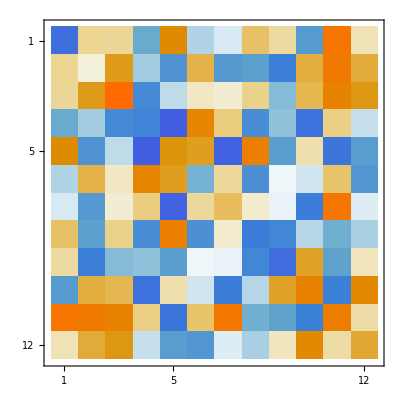
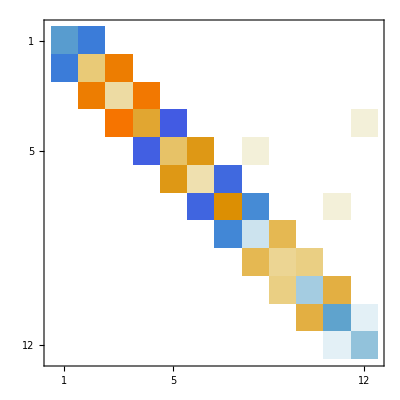
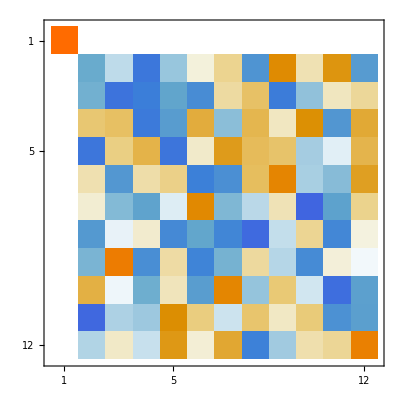

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
{Q,T}=HessenbergDecomposition[A];
Map[MatrixPlot,{A,T,Q}]
```

```mathematica
Norm[T-Qᵀ.A.Q]
Norm[Eigenvalues[A]-Eigenvalues[T]]
```

2.1193×10^-15

1.41866×10^-14

```mathematica
TabView[{"A"->GershgorignPic[A],"T"->GershgorignPic[T]}]
```

12

The tridiagonal matrix give tighter bounds. If we could make it more diagonal we would be able to isolate the eigenvalues.  This is the plan.  For symmetric matrices we are going to work out how to make the tridiagonal matrix more diagonal.

### General Matrix⟶Almost Upper Triangular⟶^(k→∞)UT

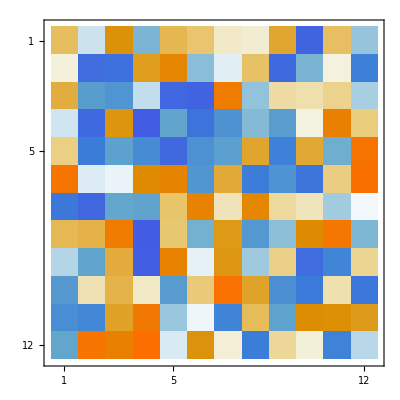
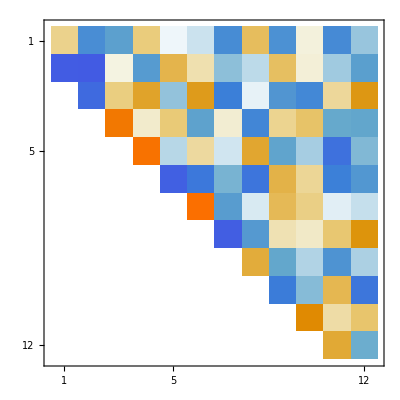
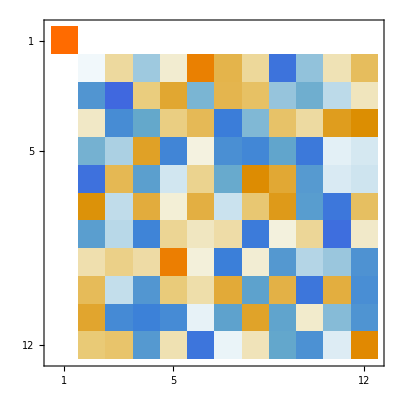

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}]; 
{Q,H}=HessenbergDecomposition[A];
Map[MatrixPlot,{A,H,Q}]
```

```mathematica
Norm[H-Qᵀ.A.Q]
Norm[A-Q.H.Qᵀ]
```

1.73713×10^-15

2.48528×10^-15

```mathematica
TabView[{"A"->GershgorignPic[A],"H"->GershgorignPic[H]}]
```

12

The almost upper triangular matrix give tighter bounds. If we could make it more upper triangular we would be able to isolate the eigenvalues.  This is the plan.  For general matrices we are going to work out how to make the almost upper triangular matrix more upper triangular.

## Localization Pic Code (From Earlier)

```mathematica
GershgorignPic[A_]:=Module[{m=Length[A],c,r1,r2},
Graphics[{
Table[
c=ReIm[A⟦i,i⟧];
r1=Sum[Abs[A⟦i,j⟧],{j,1,i-1}]+Sum[Abs[A⟦i,j⟧],{j,i+1,m}];
r2=Sum[Abs[A⟦j,i⟧],{j,1,i-1}]+Sum[Abs[A⟦i,j⟧],{j,i+1,m}];
{Hue[i/m],Opacity[0.2],EdgeForm[Hue[i/m]],
Disk[c,Min[r1,r2],{0,π/2}],
Disk[c,Min[r1,r2],{π/2,π}],
Disk[c,Min[r1,r2],{π,3π/2}],
Disk[c,Min[r1,r2],{3π/2,2π}]},
{i,m}],
Point[ReIm[Eigenvalues[A]]]},
Frame->True,
GridLines->Automatic]
]
```